# Oath Dice Odds

## Alex Rutar

In this article, we implement some of the probability computations for the combat system in the Oath board game. For more detail, see the post at https://rutar.org/writing/oath-dice-and-combat-odds/.

## Probability Computations

### General Helper Functions

These are some convenient helper functions to create the distribution and trial associations from the evaluation and probability functions. Here, a distribution is simply an association where the keys are possible outcomes, and the values are the corresponding probabilities. Here are some details on some of the functions:

- distribution: compute the distribution given a probability evaluation function and a list of possible outcomes
- experimentalDistribution: compute an experimental distribution given a trial evaluation function
- expectation: compute the expectation of a distribution
- marginal: project a multivariate distribution onto some axes
- mappedDistribution: apply a function f[x1,...,xn] to a product distribution in n dimensions.
- percentile: get the least n such that the cumulative distribution is less than or equal to n with probability pct. Automatically threads over a list.

```mathematica
distribution[pr_,outcomes_][n_]:=AssociationMap[pr[n,#]&,outcomes[n]]
experimentalDistribution[trialEval_][n_,trials_]:=KeySort@Counts@(trialEval/@RandomInteger[{1,6},{trials,n}])/trials

expectation[dist_]:=Total@KeyValueMap[#1 #2&,dist]
cumulativeDistribution[dist_]:=AssociationThread[Keys@dist,Accumulate@Values@dist]
toList[elem_List]:=elem
toList[elem_]:=List[elem]
product[distList_]:=Association[First@#->Last@#&/@Flatten[Outer[{Join@@(First/@List[##]),Times@@(Last/@List[##])}&,##,1]&@@(KeyValueMap[List,#]&/@(KeyMap[toList,#]&/@distList)),1]]
marginal[dist_,axis_]:=Total/@(Last/@#&/@GroupBy[KeyValueMap[{#1[[axis]],#2}&,dist],First])
mappedDistribution[productDist_,f_]:=Total/@(Last/@#&/@(KeySort@GroupBy[KeyValueMap[{f@@#1,#2}&,productDist],First]))

getIndex[cdf_][pct_]:=First@SelectFirst[cdf,Last@#≥pct&]
percentile[dist_,pct_Real]:=getIndex[KeyValueMap[List,cumulativeDistribution@dist]][pct]
percentile[dist_,pctList_List]:=With[{cdf=KeyValueMap[List,cumulativeDistribution@dist]},getIndex[cdf][#]&/@pctList]
```

### Defence Distributions

Let’s first set up the experimental and theoretical distributions for the defence dice.

```mathematica
defenceProbability[n_,j_]:=With[{m=IntegerExponent[j,2]},
6^(-n)Sum[Binomial[n,k]Binomial[n-k,i]Binomial[2i,j/2^k],{k,0,m},{i,0,n-k}]
]
defenceOutcomes[n_]:=Prepend[Union@@Table[2^(n-k)Range[2k],{k,0,n}],0]
defenceDistribution:=distribution[defenceProbability,defenceOutcomes]
evaluateDefenceRoll[rolls_]:=2^Count[rolls,6](Count[rolls,3|4]+2Count[rolls,5])
defenceExperimentalDistribution:=experimentalDistribution[evaluateDefenceRoll]
```

### Attack Distributions

We now set up the experimental and theoretical distributions for the attack dice.

```mathematica
attackProbability[n_,j_]:=With[{qr=QuotientRemainder[n,2]},With[{m=First@qr},
Switch[{j,qr},
{2n,_},6^(-n),
{_,{_,0}},Sum[3^(-2k)2^(3k-m-j)(Binomial[n,2k]Binomial[2k,j-m-k]+Binomial[n,2k+1]Binomial[2k+1,j-m-k]3^(-1)2),{k,0,m}],
{_,{_,1}},Sum[3^(-2k)2^(3k-m-j)(Binomial[n,2k+1]Binomial[2k+1,j-m-k-1]3^(-1)2+Binomial[n,2k]Binomial[2k,j-m-k]2^(-1)),{k,0,m}]
]
]
]

attackOutcomes[n_]:=Range[Quotient[n,2],2n]
attackDistribution:=distribution[attackProbability,attackOutcomes]
evaluateAttackRoll[rolls_]:=Floor[Count[rolls,1|2|3]/2+Count[rolls,4|5]+2Count[rolls,6]]
attackExperimentalDistribution:=experimentalDistribution[evaluateAttackRoll]
```

### Joint Distributions

Now, we compute the joint distribution for units lost in the attack along with the attack value rolled.

```mathematica
attackJointProbability[n_,{j_,l_}]:=With[{qr=QuotientRemainder[n,2]},With[{m=First@qr},
Switch[{j,l,qr},
{2n,n,_},6^(-n),
{2n,_,_},0,
{_,_,{_,0}},3^(-2(j-m-l))2^(2j-4m-3l)(Binomial[n,2(j-m-l)]Binomial[2(j-m-l),l]+(2/3)Binomial[n,2(j-m-l)+1]Binomial[2(j-m-l)+1,l]),
{_,_,{_,1}},3^(-2(j-m-l))2^(2j-4m-3l-1)((3/2)Binomial[n,2(j-m-l)-1]Binomial[2(j-m-l)-1,l]+Binomial[n,2(j-m-l)]Binomial[2(j-m-l),l])
]
]
]
disperseFirst[{a_,lst_}]:={#,a}&/@lst
attackJointOutcomes[n_]:=Join@@disperseFirst/@({#,Range[2#+Quotient[n-#,2],#+n]}&/@Range[0,n])
attackJointDistribution:=distribution[attackJointProbability,attackJointOutcomes]
evaluateJointAttackRoll[rolls_]:={evaluateAttackRoll[rolls],Count[rolls,6]}
attackJointExperimentalDistribution:=experimentalDistribution[evaluateJointAttackRoll]
```

### Unit Loss Distributions

Now, we can compute the actual unit loss distributions. This is the distribution of the number of units lost in an attack with n attackers and k defenders, assuming a defence size of nDefence. The variant unitLossNoSkullsDistribution gives the corresponding probabilities if the attacker is using a card modifier which prevents units lost from rolling skulls.

The variant unitDifferenceMap simply computes the difference between the attack power and defence power, plus 1: the attacker still must sacrifice a number of units equal to the defence force, along with any skulls.

```mathematica
unitLossMap[nDefence_][u_,v_,w_]:=v+Max[nDefence+w-u+1,0]
unitLossDistribution[n_,k_,nDefence_]:=mappedDistribution[product[{attackJointDistribution[n],defenceDistribution[k]}],unitLossMap[nDefence]]

unitLossNoSkullsMap[nDefence_][u_,w_]:=Max[nDefence+w-u+1,0]
unitLossNoSkullsDistribution[n_,k_,nDefence_]:=mappedDistribution[product[{attackDistribution[n],defenceDistribution[k]}],unitLossNoSkullsMap[nDefence]]

unitDifferenceMap[u_,w_]:=w-u+1
unitDifferenceDistribution[n_,k_]:=mappedDistribution[product[{attackDistribution[n],defenceDistribution[k]}],unitDifferenceMap]

survivingUnitHelper[dist_][n_,k_,nAttack_,nDefence_]:=With[{cdf=cumulativeDistribution[dist[n,k,nDefence]]},
KeyDrop[KeyMap[Max[nAttack-#,-1]&,cdf],-1]
]
survivingUnitCumulativeDistribution:=survivingUnitHelper[unitLossDistribution]
survivingUnitNoSkullsCumulativeDistribution:=survivingUnitHelper[unitLossNoSkullsDistribution]
```

## Examples

### Basic testing and verification

First, let' s compare the distributions for the experimental and exact distributions for the defence and attack dice. The differences should be small:

```mathematica
N/@(defenceExperimentalDistribution[5,1000000]-defenceDistribution[5])
N/@(attackExperimentalDistribution[7,1000000]-attackDistribution[7])
```

<|0→0.000272,1→-0.000108132,2→-0.000198593,3→0.000128473,4→0.0000196831,5→0.000134313,6→0.000515045,7→0.0000308683,8→-0.000488963,9→0.0000209918,10→-0.00027293,12→0.000313605,14→-0.000105033,16→-0.000246226,20→8.95062×10^-6,24→-0.0000100412,32→-0.0000140123|>

<|3→2.5×10^-6,4→0.00024,5→-0.0000396975,6→-0.000749671,7→0.000258707,8→0.000197686,9→0.0000387634,10→0.0000179707,11→3.41129×10^-6,12→0.0000219143,13→8.98857×10^-6,14→-5.72245×10^-7|>

We can do the same for the joint attack distribution:

```mathematica
N/@(attackJointDistribution[3]-attackJointExperimentalDistribution[3,1000000])
```

<|{1,0}→-0.000446,{2,0}→-0.000420333,{3,0}→-0.000247963,{3,1}→0.000697667,{4,1}→0.000301556,{4,2}→-0.0000243333,{5,2}→0.000186778,{6,3}→-0.0000473704|>

We can also compare the attack distributions to the joint distributions. By summing over all possible unit loss numbers, we should obtain the attack distribution. This is done using the marginal function. Let’s check all values between 0 and 50:

```mathematica
Table[AllTrue[attackDistribution[n]-marginal[attackJointDistribution[n],1],#==0&],{n,0,50}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Visualizing distributions

Now, we can visualize the cumulative distribution for a dice roll of 8:

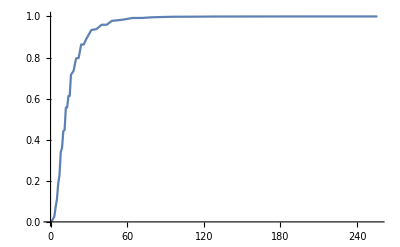

```mathematica
ListLinePlot@cumulativeDistribution@defenceDistribution@8
```

We can also visualize the unit loss distribution:

```mathematica
Manipulate[ListLinePlot[cumulativeDistribution@unitLossDistribution[n,k,nDefence],PlotRange->All,GridLines->Automatic],
{{n,10},1,20,1},
{{k,6},1,15,1},
{{nDefence,k},1,20,1}
]
```

### Computing percentile tables and other information

Now, let’s compute some nice tables with percentiles:

```mathematica
Map[formatList,Table[percentile[unitLossDistribution[n,k],{0.5,0.9,0.99}],{n,1,10},{k,1,6}],{2}]//TableForm
```

1, 2, 3 | 2, 4, 5 | 3, 6, 9 | 4, 8, 13 | 6, 12, 21 | 8, 17, 33
1, 2, 2 | 1, 3, 4 | 2, 5, 8 | 4, 8, 12 | 5, 12, 20 | 7, 16, 32
1, 1, 2 | 1, 2, 4 | 2, 4, 7 | 3, 7, 12 | 4, 11, 19 | 6, 15, 31
1, 2, 3 | 1, 2, 3 | 1, 3, 6 | 2, 6, 11 | 4, 10, 19 | 6, 14, 30
1, 2, 3 | 1, 2, 3 | 1, 3, 6 | 2, 5, 10 | 3, 9, 18 | 5, 14, 30
1, 2, 3 | 1, 2, 3 | 1, 3, 5 | 2, 5, 10 | 2, 8, 17 | 4, 13, 29
1, 2, 4 | 1, 2, 4 | 1, 3, 4 | 2, 4, 9 | 2, 8, 17 | 3, 12, 28
1, 3, 4 | 1, 3, 4 | 1, 3, 4 | 2, 4, 8 | 2, 7, 16 | 3, 11, 27
1, 3, 4 | 1, 3, 4 | 1, 3, 4 | 2, 4, 7 | 2, 6, 15 | 3, 11, 27
2, 3, 5 | 2, 3, 5 | 2, 3, 5 | 2, 4, 7 | 2, 5, 14 | 3, 10, 26

Here are come convenient helper functions to generate HTML tables using the above data:

```mathematica
wrapTag[stringList_,tag_]:=StringJoin["<",tag,">",#,"</",tag,">"]&/@stringList
asHTMLTable[entries_,rowHeaders_,columnHeaders_]:=With[{rowTags=wrapTag[Prepend[rowHeaders,""],"th"],columnTags=wrapTag[columnHeaders,"th"]},With[{entryList=wrapTag[StringJoin/@ArrayFlatten[{{List/@rowTags,Prepend[wrapTag[#,"td"]&/@entries,columnTags]}}],"tr"]},
"<table>"<>"<thead>"<>First@entryList<>"</thead>"<>"<tbody>"<>StringJoin@Rest@entryList<>"</tbody>"<>"</table>"
]
]
formatList[lst_]:=StringRiffle[ToString/@lst,", "]
getDiceTableDifference[nAttack_,nDefence_]:=asHTMLTable[
Map[formatList,Table[percentile[unitDifferenceDistribution[n,k],{0.5,0.9,0.99}],{n,1,nAttack},{k,1,nDefence}],{2}],
ToString/@Range[nAttack],
ToString/@Range[nDefence]
]
getDiceTableCount[nAttack_,nDefence_,defenceCount_]:=asHTMLTable[
Map[formatList,Table[percentile[unitLossDistribution[n,k,defenceCount],{0.5,0.9,0.99}],{n,1,nAttack},{k,1,nDefence}],{2}],
ToString/@Range[nAttack],
ToString/@Range[nDefence]
]
```

And the corresponding table HTML code, for the probabilities when ignoring skulls:

```mathematica
getDiceTableCount[25,12,8]
```

### Summarizing Combat

Finally, let’s print some information about the cumulative distribution for the number of surviving attacking units:

```mathematica
combatSummaryHelper[dist_,msg_][n_,k_,nAttack_,nDefence_]:=msg<>"\n"<>StringJoin@KeyValueMap[StringTemplate["`unitRem`: `prob`%\n"][<|"unitRem"->#1,"prob"->N[100*#2,4]|>]&,dist[n,k,nAttack,nDefence]]
combatSummary[n_,k_,nAttack_,nDefence_]:=StringJoin[
combatSummaryHelper[survivingUnitCumulativeDistribution,"# units remaining"][n,k,nAttack,nDefence],
"\n",
combatSummaryHelper[survivingUnitNoSkullsCumulativeDistribution,"# units remaining (ignore skulls)"][n,k,nAttack,nDefence]
]
```

```mathematica
combatSummary[15,6,13,3]
```

# units remaining
13: 2.995%
12: 14.86%
11: 35.2%
10: 55.13%
9: 69.65%
8: 79.0%
7: 83.69%
6: 85.88%
5: 88.18%
4: 91.0%
3: 92.71%
2: 93.29%
1: 93.97%
0: 95.0%

# units remaining (ignore skulls)
13: 68.72%
12: 73.83%
11: 78.07%
10: 81.6%
9: 84.56%
8: 87.04%
7: 89.13%
6: 90.92%
5: 92.39%
4: 93.53%
3: 94.39%
2: 95.1%
1: 95.74%
0: 96.35%